Syntax::sntxb: Expression cannot begin with "'Aula5-Exercícios'".

```mathematica
"Aula 5";


reversedSquares = Reverse[Table[n^2, {n, 1, 10}]]
```

{100,81,64,49,36,25,16,9,4,1}

```mathematica
totalFirst10Squares = Total[Table[n^2, {n, 1, 10}]]
```

385

```mathematica
first10Squares = Table[n^2, {n, 1, 10}]
ListLinePlot[first10Squares, 
 PlotMarkers → Automatic, 
 PlotLabel → "First 10 Squares", 
 AxesLabel → {"Number", "Square"}]
```

{1,4,9,16,25,36,49,64,81,100}

-Graphics-

```mathematica
sortedJoinedRange = Sort[Join[Range[1, 4], Range[1, 4]]]
```

{1,1,2,2,3,3,4,4}

```mathematica
range10to20 = Range[10, 20]
```

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
first5Squares = Table[n^2, {n, 1, 5}]
first5Cubes = Table[n^3, {n, 1, 5}]
combinedSorted = Sort[Join[first5Squares, first5Cubes]]
```

{1,4,9,16,25}

{1,8,27,64,125}

{1,1,4,8,9,16,25,27,64,125}

```mathematica
numDigits2Pow128 = IntegerLength[2^128]
```

39

```mathematica
firstDigit2Pow32 = IntegerDigits[2^32][[1]]
```

4

```mathematica
first10Digits2Pow100 = Take[IntegerDigits[2^100], 10]
```

{1,2,6,7,6,5,0,6,0,0}

```mathematica
largestDigit2Pow10 = Max[IntegerDigits[2^10]]
```

4

```mathematica
numZeros2Pow1000 = Count[IntegerDigits[2^1000], 0]
```

28

```mathematica
sortedDigits2Pow20 = Sort[IntegerDigits[2^20]]
secondSmallestDigit2Pow20 = sortedDigits2Pow20[[2]]
```

{0,1,4,5,6,7,8}

1

```mathematica
digits2Pow128 = IntegerDigits[2^128]
ListLinePlot[digits2Pow128, 
 PlotMarkers -> Automatic, 
 PlotLabel -> "Digits in 2^128", 
 AxesLabel -> {"Position", "Digit"}]
```

{3,4,0,2,8,2,3,6,6,9,2,0,9,3,8,4,6,3,4,6,3,3,7,4,6,0,7,4,3,1,7,6,8,2,1,1,4,5,6}

-Graphics-

```mathematica
sequence11to20 = Take[Range[100], {11, 20}]
```

{11,12,13,14,15,16,17,18,19,20}

```mathematica
"aula 6";


repeatedList = ConstantArray[1000, 5]
```

{1000,1000,1000,1000,1000}

```mathematica
cubesTable = Table[n^3, {n, 10, 20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

```mathematica
squares = Table[n^2, {n, 1, 20}]
ListLinePlot[squares, 
 PlotMarkers -> Automatic, 
 PlotLabel -> "First 20 Squares", 
 AxesLabel -> {"Number", "Square"}]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

-Graphics-

```mathematica
evenNumbers = Table[2*n, {n, 1, 10}]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
range10WithTable = Table[n, {n, 1, 10}]
```

{1,2,3,4,5,6,7,8,9,10}

{1,4,9,16,25,36,49,64,81,100}

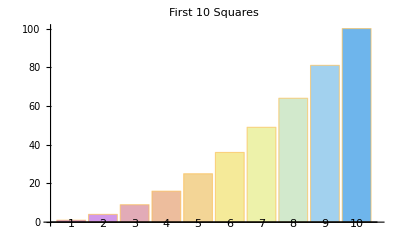

```mathematica
first10Squares = Table[n^2, {n, 1, 10}]
BarChart[first10Squares, 
 ChartLabels -> Range[1, 10], 
 ChartStyle -> "Pastel", 
 PlotLabel -> "First 10 Squares"]
```

```mathematica
digitsTable = Table[IntegerDigits[n^2], {n, 1, 10}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

```mathematica
lengthOfDigits = Table[Length[IntegerDigits[n^2]], {n, 1, 100}]
ListLinePlot[lengthOfDigits, 
 PlotMarkers -> Automatic, 
 PlotLabel -> "Length of Digits in First 100 Squares", 
 AxesLabel -> {"Number", "Length of Digits"}]
```

{1,1,1,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5}

-Graphics-

```mathematica
firstDigitTable = Table[First[IntegerDigits[n^2]], {n, 1, 20}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

```mathematica
firstDigits = Table[First[IntegerDigits[n^2]], {n, 1, 100}]
ListLinePlot[firstDigits, 
 PlotMarkers -> Automatic, 
 PlotLabel -> "First Digits of First 100 Squares", 
 AxesLabel -> {"Number", "First Digit"}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4,4,4,5,5,6,6,7,7,8,9,9,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,5,5,5,5,5,5,5,6,6,6,6,6,6,7,7,7,7,7,7,8,8,8,8,8,9,9,9,9,9,1}

-Graphics-